```mathematica
F1=√((Fx^2+Fy^2)1/4 f^2+Fx^2(1-f))
F2=√((Fx^2+Fy^2)1/4 f^2+Fy^2(1-f))
```

√((1-f) Fx^2+1/4 f^2 (Fx^2+Fy^2))

√((1-f) Fy^2+1/4 f^2 (Fx^2+Fy^2))

```mathematica
sf=Solve[E0==F1+F2,f]
```

{{f→(E0^2 Fx^2-Fx^4+E0^2 Fy^2+2 Fx^2 Fy^2-Fy^4-√(E0^6 Fx^2-2 E0^4 Fx^4+E0^2 Fx^6+E0^6 Fy^2-E0^2 Fx^4 Fy^2-2 E0^4 Fy^4-E0^2 Fx^2 Fy^4+E0^2 Fy^6))/(E0^2 Fx^2-Fx^4+E0^2 Fy^2+2 Fx^2 Fy^2-Fy^4)},{f→(E0^2 Fx^2-Fx^4+E0^2 Fy^2+2 Fx^2 Fy^2-Fy^4+√(E0^6 Fx^2-2 E0^4 Fx^4+E0^2 Fx^6+E0^6 Fy^2-E0^2 Fx^4 Fy^2-2 E0^4 Fy^4-E0^2 Fx^2 Fy^4+E0^2 Fy^6))/(E0^2 Fx^2-Fx^4+E0^2 Fy^2+2 Fx^2 Fy^2-Fy^4)}}

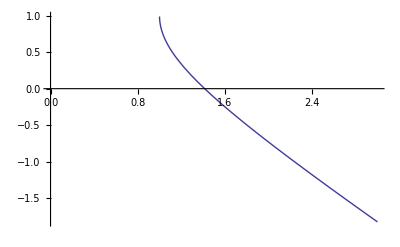

```mathematica
Plot[Evaluate[sf[[1,1,2]]/.{Fx->1/(√2),Fy->1/(√2)}],{E0,0,3}]
```

```mathematica
CForm[sf[[2,1,2]]]
```

(Power(E0,2)*Power(Fx,2) - Power(Fx,4) + Power(E0,2)*Power(Fy,2) + 
     2*Power(Fx,2)*Power(Fy,2) - Power(Fy,4) + 
     Sqrt(Power(E0,6)*Power(Fx,2) - 2*Power(E0,4)*Power(Fx,4) + 
       Power(E0,2)*Power(Fx,6) + Power(E0,6)*Power(Fy,2) - 
       Power(E0,2)*Power(Fx,4)*Power(Fy,2) - 
       2*Power(E0,4)*Power(Fy,4) - 
       Power(E0,2)*Power(Fx,2)*Power(Fy,4) + Power(E0,2)*Power(Fy,6)
       ))/(Power(E0,2)*Power(Fx,2) - Power(Fx,4) + 
     Power(E0,2)*Power(Fy,2) + 2*Power(Fx,2)*Power(Fy,2) - 
     Power(Fy,4))